# Sample Distribution

Normal Distribution

```mathematica
n=NormalDistribution[0.5,0.1]
```

NormalDistribution[0.5,0.1]

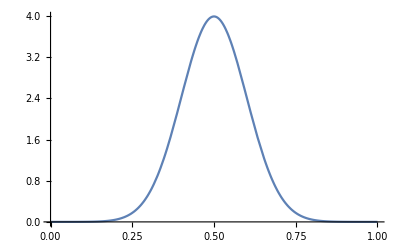

```mathematica
Plot[PDF[n,x],{x,0,1}]
```

```mathematica
n
```

NormalDistribution[0.5,0.1]

Population

```mathematica
Population=Table[RandomVariate[n],{i,1,1000}];
```

```mathematica
Mean[Population]
```

0.504084

```mathematica
Variance[Population]
```

0.0098354

Sample

```mathematica
Sample=Table[Mean[Table[RandomVariate[n],{i,1,1000}]],{i,1,100}];
```

```mathematica
Mean[Sample]
```

0.499899

```mathematica
Variance[Sample]
```

9.61351×10^-6

```mathematica
0.01/1000
```

0.00001